```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out", "schaeferTurek"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/schaeferTurek

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
getSizes[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,4] &/@StringCases[thelist, RegularExpression["size([0-9]*)"]]] 
sizes = getSizes[srts];
permutations = Ordering[sizes];
sizes = sizes[[permutations]];
cumulants = cumulants[[permutations]];
srts = srts[[permutations]];
```

```mathematica
dragData[input_] := Drop[Map[Delete[#,3]&,input],1000];
liftData[input_] := Drop[Map[Delete[#,2]&,input],1000];
valuesOnly[data_]:=Flatten[Map[Delete[#,1]&,data]];

dataFrequency[list_] := Abs[Fourier[ #[[2]]&/@list]];

maximaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],-2];
minimaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],2]

lastWavelimits[data_]:=Flatten[ Take[maximaPositions[data],-2]];
lastWavelength[data_]:=Differences[lastWavelimits[data]][[1]];

lastWave[data_]  := Take[data,lastWavelimits[data]];

means[datas_] := Map[Mean[valuesOnly[#]]&,datas];
bothMeansPlotReady[filterFunction_] := {Transpose[{sizes,means[filterFunction /@ Import /@ cumulants]}],Transpose[{sizes,means[filterFunction /@ Import /@ srts]}]};
```

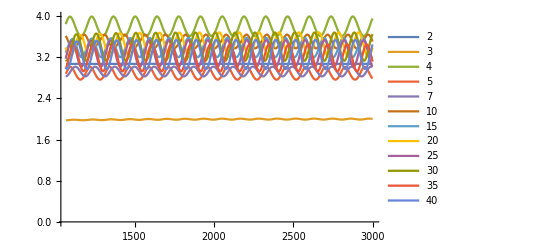

```mathematica
ListLinePlot[dragData /@Import /@ cumulants , PlotLegends->sizes]
```

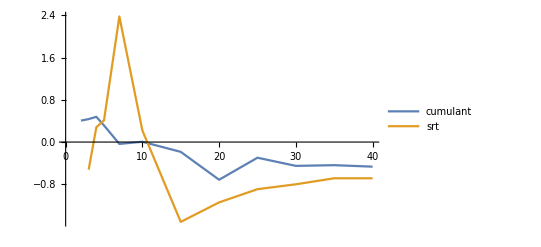

```mathematica
ListLinePlot[bothMeansPlotReady[liftData], PlotLegends->{"cumulant","srt"}]
```

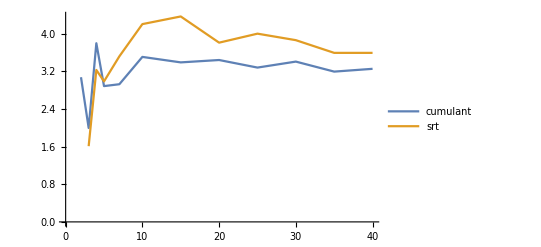

```mathematica
ListLinePlot[bothMeansPlotReady[dragData], PlotLegends->{"cumulant","srt"}]
```

```mathematica
SetDirectory[FileNameJoin[{ParentDirectory[NotebookDirectory[]],"out", "schaeferTurek"}]]
```

/home/florian/Projects/university/masters_thesis/code/2D/out/schaeferTurek

```mathematica
srts = Complement[FileNames[], FileNames["*time"], FileNames["cumulant*"]];
cumulants = Complement[FileNames[], FileNames["*time"], FileNames["srt*"]];
getSizes[thelist_]:=Read[StringToStream[#],Number]&/@Flatten[ StringDrop[#,4] &/@StringCases[thelist, RegularExpression["size([0-9]*)"]]] 
sizes = getSizes[srts];
permutations = Ordering[sizes];
sizes = sizes[[permutations]];
cumulants = cumulants[[permutations]];
srts = srts[[permutations]];
```

```mathematica
dragData[input_] := Drop[Map[Delete[#,3]&,input],1000];
liftData[input_] := Drop[Map[Delete[#,2]&,input],1000];
valuesOnly[data_]:=Flatten[Map[Delete[#,1]&,data]];

dataFrequency[list_] := Abs[Fourier[ #[[2]]&/@list]];

maximaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],-2];
minimaPositions[list_] :=1+Position[Differences[Sign[Differences[list[[All,2]]]]],2]

lastWavelimits[data_]:=Flatten[ Take[maximaPositions[data],-2]];
lastWavelength[data_]:=Differences[lastWavelimits[data]][[1]];

lastWave[data_]  := Take[data,lastWavelimits[data]];

means[datas_] := Map[Mean[valuesOnly[#]]&,datas];
bothMeansPlotReady[filterFunction_] := {Transpose[{sizes,means[filterFunction /@ Import /@ cumulants]}],Transpose[{sizes,means[filterFunction /@ Import /@ srts]}]};
```

```mathematica
ListLinePlot[dragData /@Import /@ cumulants , PlotLegends->sizes]
```

-Graphics-

```mathematica
ListLinePlot[bothMeansPlotReady[liftData], PlotLegends->{"cumulant","srt"}]
```

-Graphics-

```mathematica
ListLinePlot[bothMeansPlotReady[dragData], PlotLegends->{"cumulant","srt"}]
```

-Graphics-